```mathematica
(*** Fighting Fantasy combat analysis -- visualising heuristic good strategies ***)
```

```mathematica
(*** read in results from heuristic simulation ***)
```

```mathematica
f = Table[Number, {i, 1, 16}];
```

```mathematica
list = ReadList["heuristic.txt", f];
```

```mathematica
(*** choose which parameterisations to plot ***)
```

```mathematica
lset = {13, 12, 10, 9, 7, 0};
dset = {-4, -2, 0, 2, 4};
lset = {0,12, 9, 6,3};
```

```mathematica
(*** set graphical choices ***)
```

```mathematica
gset = Table[Table[{}, {i, 1, Length[lset]}], {j, 1, Length[dset]}];
```

```mathematica
myHue[x_]:=Lighter[ColorData["ThermometerColors"][x]]
```

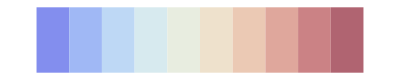

```mathematica
Graphics[Table[{myHue[i/10],Rectangle[{i,0},{i+1,1}]}, {i, 1, 10}]]
```

```mathematica
(*** construct summary plots of best heuristic strategy and victory probability ***)
```

```mathematica
For[di=1,di≤Length[dset],di++,
For[li=1, li ≤ Length[lset], li++,
d= dset[[di]];
l = lset[[li]];
set = {};
For[i = 1, i ≤ Length[list], i++,
If[list[[i]][[1]] == d && list[[i]] [[4]] == l, AppendTo[set, {list[[i]][[2]], list[[i]][[3]], list[[i]][[14]], list[[i]][[15]], list[[i]][[5]]}];
];
];
g = {(*Black,Text["shero", {12,-1}], Text["sopp", {-2,12}], Text["kdiff = "<>ToString[d]<>" lhero = "<>ToString[l],{12, 27}],*)Table[{myHue[set[[i]][[3]]],Rectangle[{set[[i]][[1]]-0.5, set[[i]][[2]]-0.5},{set[[i]][[1]]+0.5, set[[i]][[2]]+0.5}], If[l ≠ 0&&set[[i]][[3]] > 1.05*set[[i]][[5]],{GrayLevel[set[[i]][[4]]/9], Text[set[[i]][[4]], {set[[i]][[1]], set[[i]][[2]]}]}]}, {i, 1, Length[set]}]};
gset[[di]][[li]] =Graphics[g];
];
];
```

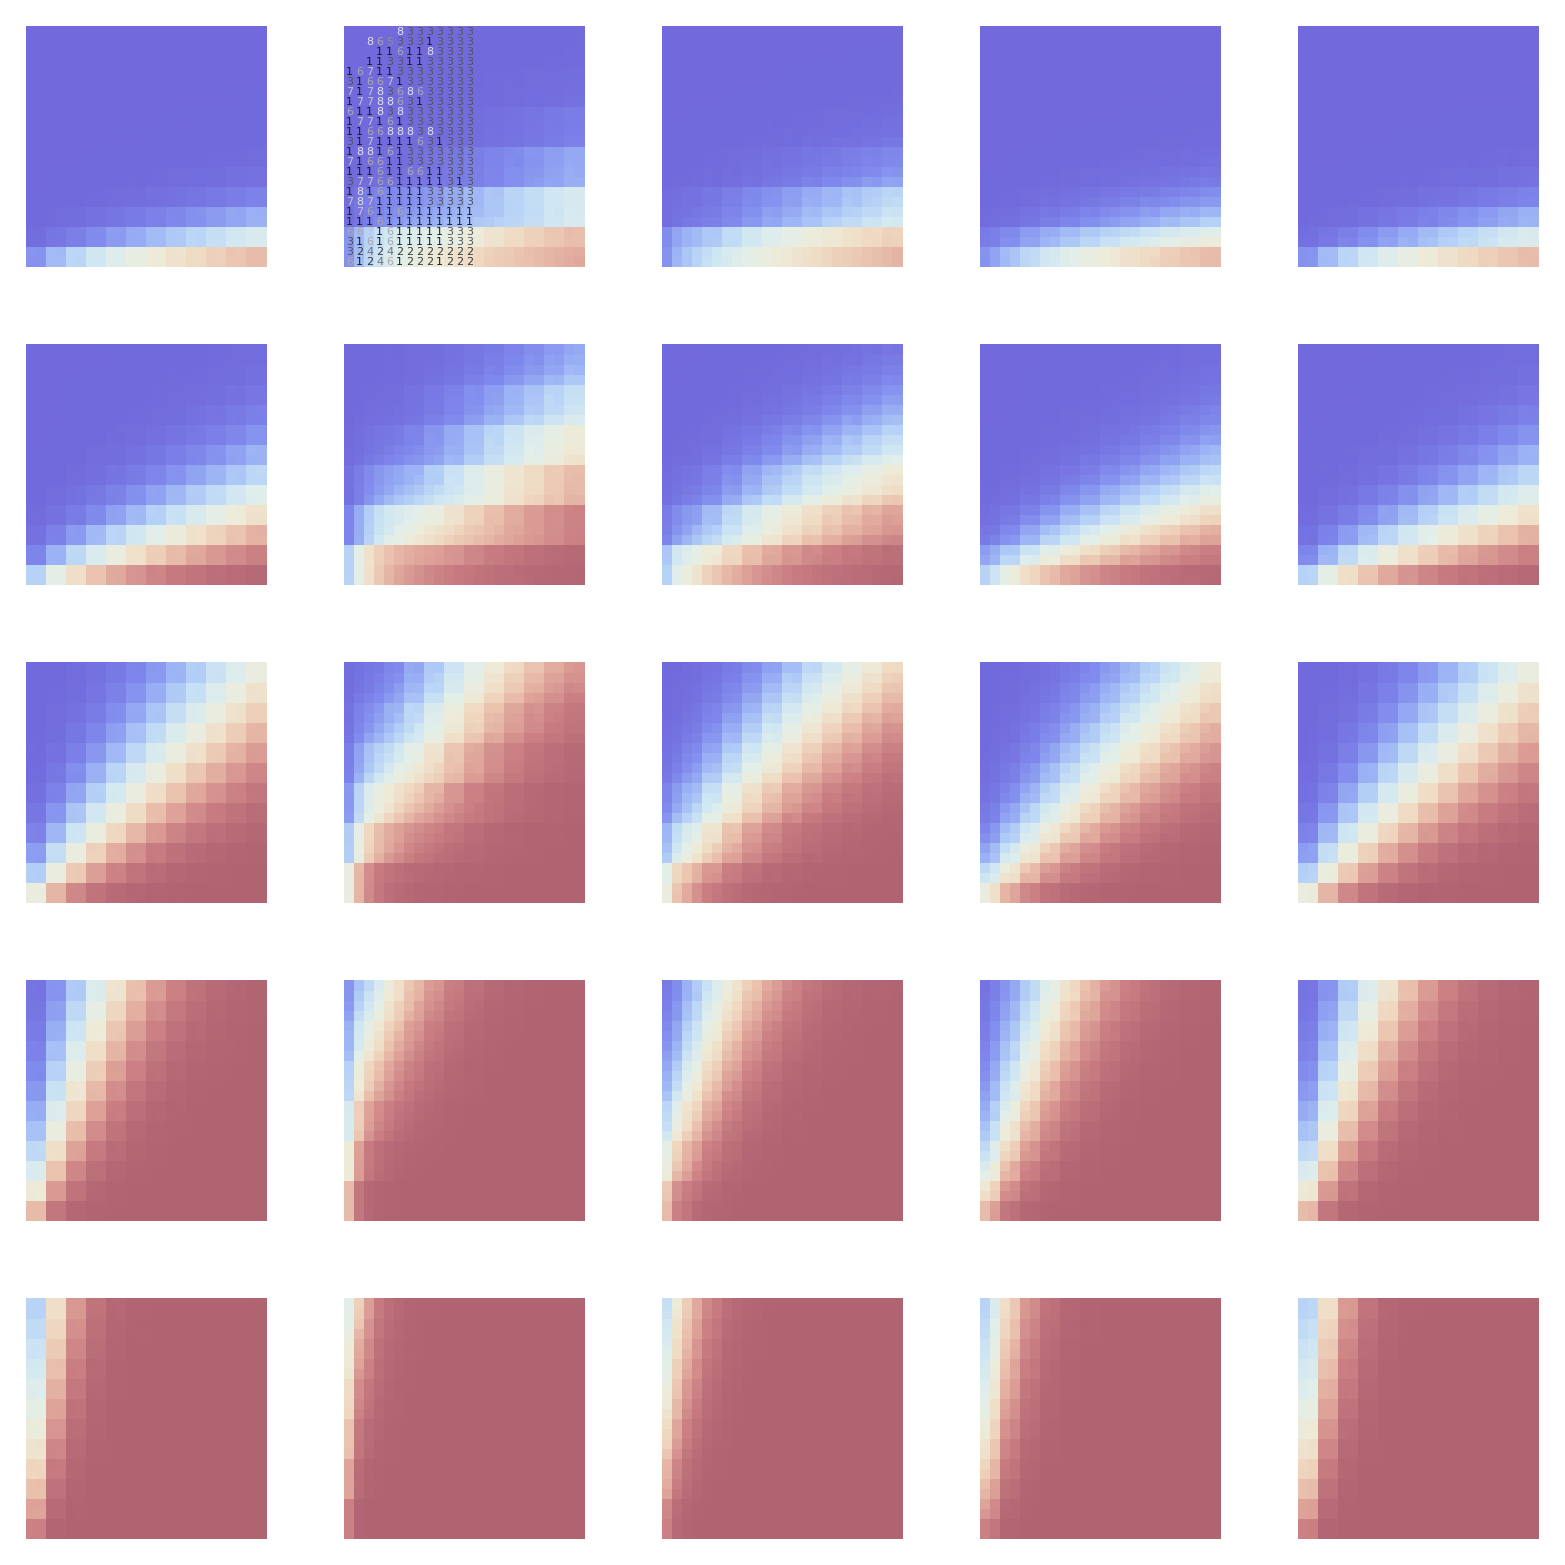

```mathematica
GraphicsGrid[gset]
```

```mathematica
Export["heuristic-1.svg", GraphicsGrid[gset], ImageSize->1000]
```

heuristic-1.svg

```mathematica
(*** other plot formats ***)
```

```mathematica
dset = {-4, 0, 4};
lset = {12};
```

```mathematica
gset = Table[Table[{}, {i, 1, Length[lset]}], {j, 1, Length[dset]}];
```

```mathematica
For[di=1,di≤Length[dset],di++,
For[li=1, li ≤ Length[lset], li++,
d= dset[[di]];
l = lset[[li]];
set = {};
For[i = 1, i ≤ Length[list], i++,
If[list[[i]][[1]] == d && list[[i]] [[4]] == l, AppendTo[set, {list[[i]][[2]], list[[i]][[3]], list[[i]][[5]], list[[i]][[6]], list[[i]][[7]], list[[i]][[8]]}];
];
];
g = Table[{Black,Text["shero", {40*(j-3)+12,-1}], Text["sopp", {40*(j-3)+-2,12}], Text["kdiff = "<>ToString[d]<>" lhero = "<>ToString[l]<>"\nStrategy "<>ToString[j-3],{40*(j-3)+12, 27}],Table[{myHue[set[[i]][[j]]],Rectangle[{40*(j-3)+set[[i]][[1]]-0.5, set[[i]][[2]]-0.5},{40*(j-3)+set[[i]][[1]]+0.5, set[[i]][[2]]+0.5}]}, {i, 1, Length[set]}]}, {j, 3, 6}];
gset[[di]][[li]] =Graphics[g];
];
];
```

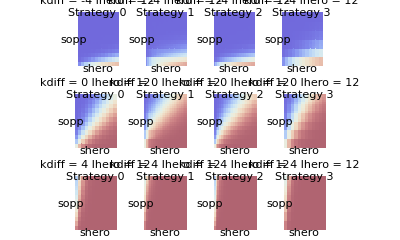

```mathematica
GraphicsGrid[gset]
```

```mathematica
Export["heuristic-2.svg", GraphicsGrid[gset], ImageSize->1000]
```

~/Dropbox/Documents/2019_Projects/FF/Fix/presentluckopen2.svg

```mathematica
dset = {-4, 0, 4};
lset = {9};
```

```mathematica
gset = Table[Table[{}, {i, 1, Length[lset]}], {j, 1, Length[dset]}];
```

```mathematica
For[di=1,di≤Length[dset],di++,
For[li=1, li ≤ Length[lset], li++,
d= dset[[di]];
l = lset[[li]];
set = {};
For[i = 1, i ≤ Length[list], i++,
If[list[[i]][[1]] == d && list[[i]] [[4]] == l, AppendTo[set, {list[[i]][[2]], list[[i]][[3]], list[[i]][[5]], list[[i]][[6]], list[[i]][[7]], list[[i]][[8]]}];
];
];
g = Table[{Black,Text["shero", {40*(j-3)+12,-1}], Text["sopp", {40*(j-3)+-2,12}], Text["kdiff = "<>ToString[d]<>" lhero = "<>ToString[l]<>"\nStrategy "<>ToString[j-3],{40*(j-3)+12, 27}],Table[{myHue[set[[i]][[j]]],Rectangle[{40*(j-3)+set[[i]][[1]]-0.5, set[[i]][[2]]-0.5},{40*(j-3)+set[[i]][[1]]+0.5, set[[i]][[2]]+0.5}]}, {i, 1, Length[set]}]}, {j, 3, 6}];
gset[[di]][[li]] =Graphics[g];
];
];
```

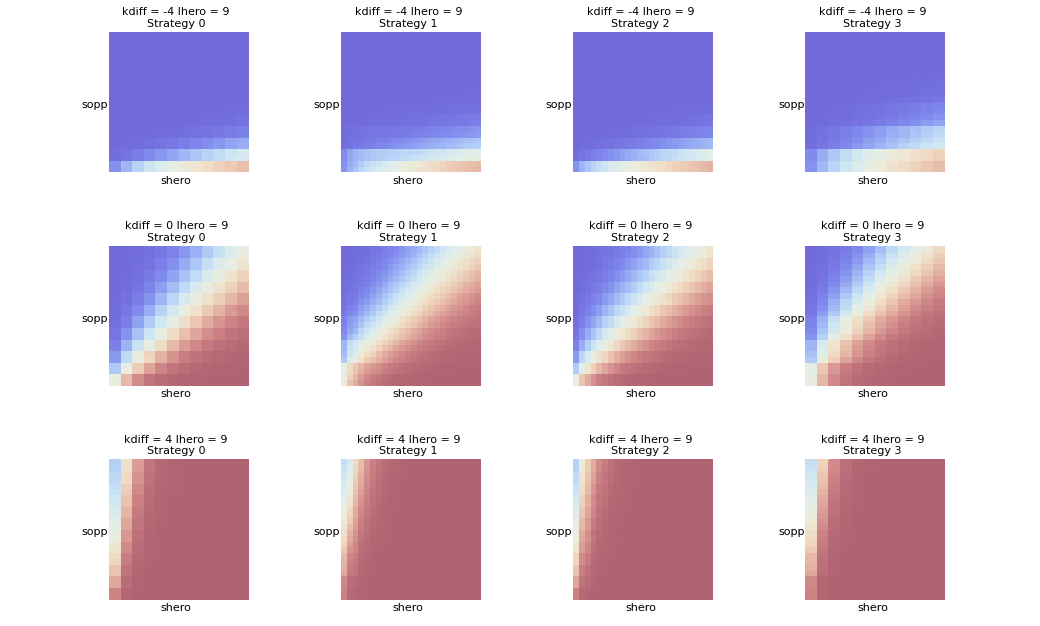

```mathematica
GraphicsGrid[gset]
```

```mathematica
Export["heuristic-3.svg", GraphicsGrid[gset], ImageSize->1000]
```

~/Dropbox/Documents/2019_Projects/FF/presentluckopen2a.svg